```mathematica
ClearAll["Global`*"]
DSolve[T'[t] == (Q/(ρ*cp*V) - k/(ρ*cp*V*L)T[t])A, T[t], t]
Solve[(L*Q)/k*ⅇ^((-t*k*A)/(ρ*cp*L*V))== 0.25, t]
Solve[k == (Q*L)/T(1-ⅇ^((-t*k)/(ρ*L*V*cp))), k]
```

{{T[t]→(L Q)/k+ⅇ^(-(A k t)/(cp L V ρ)) C[1]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-(1. cp L V ρ Log[(0.25 k)/(L Q)])/(A k)}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→(L (Q t+cp T V ρ ProductLog[-(ⅇ^(-(Q t)/(cp T V ρ)) Q t)/(cp T V ρ)]))/(t T)}}

```mathematica
k = 0.076;
ρ = 2.7 ;
cp = 0.9;
V = 0.0154 * 0.4 * 100^2;
L = 0.01;
A = 0.0154;
Tamb = 27.5;
Tw = 5;
T[t_, Q_] = (L* Q)/k+ⅇ^(-(A k t*3600)/(cp L V ρ)) *(Tamb - (L*Q)/k)
Terror[t_, Q_] = ((L*Q)/k+Tw-Tamb)ⅇ^((-t*3600*k*A)/(ρ*cp*V*L))
```

ⅇ^(-2.81481 t) (27.5-0.131579 Q)+0.131579 Q

ⅇ^(-2.81481 t) (-22.5+0.131579 Q)

```mathematica
NSolve[T[t, 18.32*0.32 /0.0141]== 50, t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.623283}}

```mathematica
α[t_] = T[t]/(L*Q/k)
```

0.768884 ⅇ^(-1.85185 t)

```mathematica
α[3]
```

0.00297244

```mathematica
T[1, 18.4*0.32/0.0141]
```

53.3014

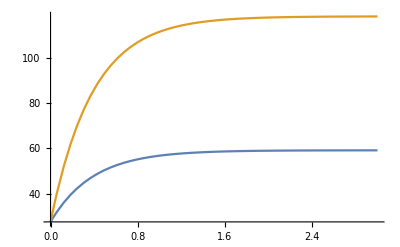

```mathematica
Plot[{T[t,(18.22*0.32/0.0141)], T[t, 2*(18.22*0.32/0.0141)]}, {t, 0, 3}]
```

```mathematica
1/0.05 0.9*0.0154*0.4*100^2*2.7*Log[(18.22*0.32)/(0.0154*0.25*0.05)]/3600
```

8.58086